```mathematica
(* For Exporting *)
SetDirectory[NotebookDirectory[]];

bin=Databin["66W7CW2x"];

(* Take the arbitrary number stored and convert it to a DaetObject, then a string *)
times=Normal[DateString/@(DateObject/@Dataset[bin][All,"Timestamp"])];
(* Use the names from the last row to be sure to have them all *)
names=Select[Keys[Dataset[bin][Length[Dataset[bin]]]]//Normal,StringContainsQ[#,"("]&];
Clear[data]
data=ToExpression[names/.(Dataset[bin][All,names]//Normal)];
dayTimes=N[(AbsoluteTime[#]-AbsoluteTime[times[[Length[times]]]])/(3600*24)]&/@times;

(* This may not work when a new candidate is added now... *)
InvalidNum=-1;
data=Module[{emptyData},

emptyData=Table[Table[

If[Or[Length[data[[j]]]<i,
StringLength[ToString[data[[j,i]]]]==0],
InvalidNum,data[[j,i]]]

,{i,Length[names]}],{j,Length[data]}]];
(* This one will be better... *)
MissingIndices[name_String]:=Union[Flatten[Position[MissingQ/@Dataset[bin][All,name],True]]]

lastNamesWithParty=Module[{split},(split=StringSplit[#];StringJoin[split[[2]]," ",split[[3]]])&/@names];
lastNamesWithoutParty=Module[{split},(split=StringSplit[#];split[[2]])&/@names];

(* A function that finds the indices of all elements of a list of strings that contain a particular substring. *)
GetIndicesFromList[list_List,str_String]:=Module[{vals},
vals=Select[list,StringContainsQ[#,str]&];
Flatten[Union[Position[list,#]&/@vals]
]]
(* Republican and Democrat indices. *)
reps=GetIndicesFromList[names,"(R)"];
dems=GetIndicesFromList[names,"(D)"];
(* convert a data set where each row of data was taken at the same time *)
ConvertToTimes[data_List,times_List]:=If[Length[data]≠Length[times],Message[ConvertToTimes::illegal],
Table[TimeSeries[Table[{times[[i]],data[[i,j]]},{i,Length[times]}]],{j,Length[data[[1]]]}]]
absoluteDiffData=Table[data[[i+1]]-data[[i]],{i,1,Length[data]-1}];
percentDiffData=Table[(data[[i+1]]-data[[i]])/data[[i]]//N,{i,1,Length[data]-1}];
titles={"Total Likes","Overnight Change (Absolute)","Overnight Change (Percentage)"};
pieTitles={"Total Likes (#)","Total Likes (%)","Overnight Change (#)","Overnight Change (%)"};
findIndex[candidate_String]:=Position[names,_String?(StringContainsQ[#,candidate]&)][[1,1]]

graphFn[option_Integer,selection_List,scale_Integer]:=Module[
{labels,plotLabel,graph,graphTimes,fn,styles},
labels=If[Length[selection]==Length[names],lastNamesWithParty,lastNamesWithoutParty];
plotLabel=titles[[option]];
graph=If[option==1,data,If[option==2,absoluteDiffData,percentDiffData]];
graphTimes=If[option==1,times,times[[2;;]]];
fn=If[scale==1,DateListPlot,DateListLogPlot];

fn[ConvertToTimes[graph[[All,selection]],graphTimes],PlotLegends->labels[[selection]],
PlotLabel->plotLabel,
PlotRange->All]]

pieFn[option_Integer,timestamp_Integer,selection_List]:=Module[{labels,plotLabel,graph,graphTimes,totalLikes,labelfn,ts},
plotLabel=pieTitles[[option]];
graph=If[option≤2,data,If[option==3,absoluteDiffData,percentDiffData//N]];
graphTimes=If[option≤2,times,times[[2;;]]];
labels=If[Length[selection]==Length[names],lastNamesWithParty,lastNamesWithoutParty];
ts=Min[timestamp,Length[graphTimes]];
totalLikes=Total[graph[[ts,selection]]];
labelfn=If[option==1,(Placed[Row[{NumberForm[IntegerPart[#/1000],DigitBlock->3],"k"}],"RadialCenter"]&),

If[option==3,
(Placed[Row[{NumberForm[IntegerPart[#],DigitBlock->3],""}],"RadialCenter"]&),

If[option==2,(Placed[Row[{N[#/totalLikes,3]*100,"%"}],"RadialCenter"]&),
(Placed[Row[{N[#,3]*100,"%"}],"RadialCenter"]&)
]]];

PieChart[graph[[ts,selection]],ChartLabels->Placed[labels[[selection]],"RadialCallout"],PlotLabel->plotLabel<>"\n"<>graphTimes[[ts]],
LabelingFunction->labelfn
]]

tableFn[sort_Integer,order_Integer,timestamp_Integer,selection_List]:=Module[{labels,plotLabel,graph,tableData,ordering},
plotLabel=titles[[sort]];
graph=If[sort==1,data,If[sort==2,absoluteDiffData,percentDiffData//N]];
labels=If[Length[selection]==Length[names],lastNamesWithParty,lastNamesWithoutParty];
tableData=Table[{data[[timestamp+1,i]],absoluteDiffData[[timestamp,i]],
percentDiffData[[timestamp,i]],
ToString[percentDiffData[[timestamp,i]]*100]<>"%"},{i,selection}];
ordering=If[sort==0,
Ordering[labels[[selection]]],
Ordering[tableData,All,#1[[sort]]>#2[[sort]]&]];
ordering=If[order==1,ordering,Reverse[ordering]];

Labeled[TableForm[tableData[[ordering,{1,2,4}]],TableHeadings->{labels[[selection[[ordering]]]],{"Total Likes","Overnight Gains\n(Absolute)","Overnight Gains\n(Percentage)"}}],"Likes as of "<>times[[timestamp+1]]<>"\n",Top]]
(*NewCandidate[names,times,data,"like_data.csv"]*)



(* FIXME : Need a new replacement for the NewCandidate -- base it on the MissingIndices function? *)
```

ToExpression::notstrbox: Missing["KeyAbsent", "Joe Biden (D)"] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

```mathematica
Manipulate[
graphFn[option,selection,scale],
{{option,1},
(#->titles[[#]])&/@Range[Length[titles]]},
{{selection,Range[1,Length[names]]},{Range[1,Length[names]]-> "All",reps->"Republicans",dems->"Democrats"}},
{{scale,1},{1->"Normal",2->"Log"}}
]
```

```mathematica
Manipulate[
pieFn[option,timestamp,selection],

{{option,1},
(#->pieTitles[[#]]&/@Range[Length[pieTitles]])},
{timestamp,1,If[option≤2,Length[times],Length[times]-1],1},
{{selection,Range[1,Length[names]]},{Range[1,Length[names]]-> "All",reps->"Republicans",dems->"Democrats"}}]
```

```mathematica
Manipulate[tableFn[sort,order,timestamp,selection],
{{sort,1},
Union[(#->titles[[#]])&/@Range[Length[titles]],{0->"Name"}]},
{{order,1},{1->"Descending",2->"Ascending"}},
{timestamp,1,Length[times]-1,1},
{{selection,Range[1,Length[names]]},{Range[1,Length[names]]-> "All",reps->"Republicans",dems->"Democrats"}}]
```

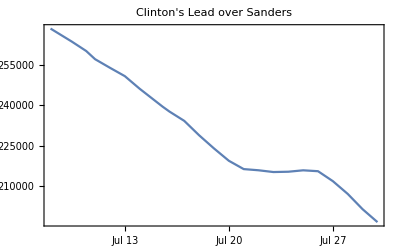

{{x→64.1535}}

```mathematica
DateListPlot[Table[{times[[i]],data[[i,findIndex["Clinton"]]]-data[[i,findIndex["Sanders"]]]},{i,6,Length[data]}],PlotLabel->"Clinton's Lead over Sanders"]
(* FIXME: Make this based on time, not index -- some days aren't at the same time*)
Solve[LinearModelFit[{dayTimes[[6;;]],data[[6;;,findIndex["Clinton"]]]-data[[6;;,findIndex["Sanders"]]]}//Transpose,{x},x]["BestFit"]==0,x]
```

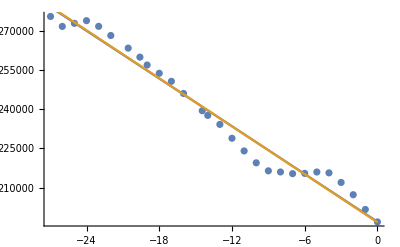

```mathematica
Show[ListPlot[{dayTimes,data[[All,findIndex["Clinton"]]]-data[[All,findIndex["Sanders"]]]}//Transpose],
Plot[{Normal[LinearModelFit[{dayTimes[[;;]],data[[;;,findIndex["Clinton"]]]-data[[;;,findIndex["Sanders"]]]}//Transpose,{x},x]]/.{x->t},
Normal[LinearModelFit[{dayTimes[[6;;]],data[[6;;,findIndex["Clinton"]]]-data[[6;;,findIndex["Sanders"]]]}//Transpose,{x},x]]/.{x->t}},{t,-Length[data],0}]
]
```

```mathematica
((#[[1]])/#[[2]]//N)&/@percentDiffData[[All,{findIndex["Sanders"],findIndex["Clinton"]}]]
```

{2.81561,1.13268,1.13681,1.97213,2.59463,2.65418,2.68433,3.00363,2.82221,2.65728,2.80926,2.05777,2.16439,2.45424,2.96975,3.38932,3.09057,2.3433,1.37053,1.49049,1.20241,1.04448,1.37509,2.89527,3.94649,3.52474,3.21272}

```mathematica
Manipulate[Labeled[TableForm[Sort[{#,(LinearModelFit[{dayTimes[[;;]],data[[;;,findIndex[#]]]}//Transpose,{x},x]["BestFit"]/.{x->time})}&/@lastNamesWithoutParty,#1[[2]]>#2[[2]]&]],
"Estimated Total Likes from Linear Fit\n"<>DatePlus[times[[Length[times]]],time]
,Top],{time,1,478,1}]
```

```mathematica
(*SetDirectory[NotebookDirectory[]];
data2=Import["like_data.csv"];
bin=Databin["66W7CW2x"];
names=data2[[1]];
data2=data2[[2;;]];
InvalidNum=-1;
emptyData=Table[Table[

If[Or[Length[data2[[j]]]<i,
StringLength[ToString[data2[[j,i]]]]==0],
InvalidNum,data2[[j,i]]]

,{i,Length[names]}],{j,Length[data2]}];
data2=emptyData;

(*  THIS IS THE IMPORTANT ONE -- HOW TO ADD IN CASE OF ERROR   *)
data2=Import["like_data.csv"];
names=data2[[1]];
DatabinAdd[bin,Association[MapThread[#1->#2&,{names,data2[[Length[data2],1;;Length[names]]]}]]]


times=(DateObject/@Dataset[bin][All,"Timestamp"]);*)
(*ResetTheDatabin[]:=For[i=0,i<Length[data],i++,DatabinRemove[bin,1]]*)
(*For[i=1,i≤Length[data],i++,DatabinAdd[bin,Association[MapThread[#1->#2&,{names,data[[i]]}]]]]*)
```

```mathematica
DatabinRemove[Databin["66W7CW2x"],30];
```